# So you wanna draw some Tori? You’ve come to the right place.

```mathematica
Torus[center_,opacity_,color_]:=ParametricPlot3D[{(2+Cos[ϕ])Cos[θ]+center[[1]],(2+Cos[ϕ])Sin[θ]+center[[2]],Sin[ϕ]},{θ,0,2π},{ϕ,0,2π},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->Large,PlotStyle->{Opacity[opacity],color}];
Torus[center_,opacity_]:=ParametricPlot3D[{(2+Cos[ϕ])Cos[θ]+center[[1]],(2+Cos[ϕ])Sin[θ]+center[[2]],Sin[ϕ]},{θ,0,2π},{ϕ,0,2π},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->Large,PlotStyle->Opacity[opacity]];
Torus[center_]:=ParametricPlot3D[{(2+Cos[ϕ])Cos[θ]+center[[1]],(2+Cos[ϕ])Sin[θ]+center[[2]],Sin[ϕ]},{θ,0,2π},{ϕ,0,2π},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->Large];
Meridian[center_,θ1_,θ2_]:=ParametricPlot3D[{(2+Cos[1*t+0*2*π])*Cos[0*t+0*2*π]+center[[1]],(2+Cos[1*t+0*2*π])*Sin[0*t+0*2*π]+center[[2]],Sin[1*t+0*2*π]},{t,θ1,θ2},PlotRange->4,PlotStyle->{Thickness[.01],Red},Boxed->False];
Meridian[center_]:=ParametricPlot3D[{(2+Cos[1*t+0*2*π])*Cos[0*t+0*2*π]+center[[1]],(2+Cos[1*t+0*2*π])*Sin[0*t+0*2*π]+center[[2]],Sin[1*t+0*2*π]},{t,0,2*π},PlotRange->4,PlotStyle->{Thickness[.01],Red},Boxed->False];
Longitudnal[center_,θ1_,θ2_]:=ParametricPlot3D[{(2+Cos[0*t+0*2*π])*Cos[1*t+0*2*π]+center[[1]],(2+Cos[0*t+0*2*π])*Sin[1*t+0*2*π]+center[[2]],Sin[0*t+0*2*π]},{t,θ1,θ2},PlotRange->4,PlotStyle->{Thickness[.01],Blue},Boxed->False];
Longitudnal[center_]:=ParametricPlot3D[{(2+Cos[0*t+0*2*π])*Cos[1*t+0*2*π]+center[[1]],(2+Cos[0*t+0*2*π])*Sin[1*t+0*2*π]+center[[2]],Sin[0*t+0*2*π]},{t,0,2*π},PlotRange->4,PlotStyle->{Thickness[.01],Blue},Boxed->False];
PunctureX[center_,color_]:=ParametricPlot3D[{h+2+center[[1]],.5*Cos[θ]/h^(1/1.001)+center[[2]],.5*Sin[θ]/h^(1/1.001)},{θ,0,2π},{h,.7,5},Mesh->None,AspectRatio->1,ImageSize->Large,PlotRange->{{-.1,.1},{0,1},{-.5,.5}},PlotPoints->50,PlotStyle->color];
PunctureX[center_]:=ParametricPlot3D[{h+2+center[[1]],.5*Cos[θ]/h^(1/1.001)+center[[2]],.5*Sin[θ]/h^(1/1.001)},{θ,0,2π},{h,.7,5},Mesh->None,AspectRatio->1,ImageSize->Large,PlotRange->{{-.1,.1},{0,1},{-.5,.5}},PlotPoints->50];
PunctureY[center_,color_]:=ParametricPlot3D[{.5*Cos[θ]/h^(1/1.001)+center[[1]],h+2+center[[2]],.5*Sin[θ]/h^(1/1.001)},{θ,0,2π},{h,.7,5},Mesh->None,AspectRatio->1,ImageSize->Large,PlotRange->{{-.1,.1},{0,1},{-.5,.5}},PlotPoints->50,PlotStyle->color];
PunctureY[center_]:=ParametricPlot3D[{.5*Cos[θ]/h^(1/1.001)+center[[1]],h+2+center[[2]],.5*Sin[θ]/h^(1/1.001)},{θ,0,2π},{h,.7,5},Mesh->None,AspectRatio->1,ImageSize->Large,PlotRange->{{-.1,.1},{0,1},{-.5,.5}},PlotPoints->50];
Boxer[dim_]:=Graphics3D[{},PlotRange->dim,Axes->False,Boxed->False,ImageSize->800];
Boxer[dim_,imSize_]:=Graphics3D[{},PlotRange->dim,Axes->False,Boxed->False,ImageSize->imSize];
```

## Genus - 2 surface with curves drawn on it

```mathematica
DoubleTorus[center_,opacity_,color_]:={Torus[center,opacity,color],Torus[center+3,opacity,color]};

DoubleTorusB[center_,color_]:=ParametricPlot3D[{(2+Cos[t])+center[[1]],0+center[[2]],Sin[t]},{t,0,2π},PlotRange->4,PlotStyle->{Thickness[.01],Red},Boxed->False];

DoubleTorusAC[center_,color_]:={ParametricPlot3D[3{Cos[t],Sin[t],0}+center,{t,π/2,5π/4},PlotRange->4,PlotStyle->{Thickness[.01],color},Boxed->False],
ParametricPlot3D[3{Cos[t],Sin[t],0}+{3,3,0}+center,{t,π,π/4},PlotRange->4,PlotStyle->{Thickness[.01],color},Boxed->False]};
DoubleTorusCA[center_,color_]:={ParametricPlot3D[3{Cos[t],Sin[t],0}+center,{t,5π/4,2π},PlotRange->4,PlotStyle->{Thickness[.01],color},Boxed->False],
ParametricPlot3D[{3Cos[t],3Sin[t],0}+center+{3,3,0},{t,3π/2,2π+π/4},PlotRange->4,PlotStyle->{Thickness[.01],color},Boxed->False]};

DoubleTorusAB[center_,color_]:=ParametricPlot3D[{(2+Cos[2π t])Cos[π-2π t]+center[[1]],(2+Cos[2π t])Sin[π-2π t]+center[[2]],Sin[2π t]},{t,0,.5},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->Large,PlotStyle->{Thickness[.01],color}];
DoubleTorusBA[center_,color_]:=ParametricPlot3D[{(2+Cos[2π t])Cos[π-2π t]+center[[1]],(2+Cos[2π t])Sin[π-2π t]+center[[2]],Sin[2π t]},{t,.5,1},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->Large,PlotStyle->{Thickness[.01],color}];

DoubleTorusAD[center_,color_]:={ParametricPlot3D[3{Cos[t],Sin[t],0}+center,{t,π/2,5π/4},PlotRange->4,PlotStyle->{Thickness[.01],color},Boxed->False],ParametricPlot3D[{(2+Cos[2π t])*Cos[π+π/2 t]+center[[1]],(2+Cos[2π t])*Sin[π+π/2 t]+center[[2]],Sin[2π t]}+{3,3,0},{t,0,.5},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->Large,PlotStyle->{Thickness[.01],color}]};
DoubleTorusDA[center_,color_]:={ParametricPlot3D[3{Cos[t],Sin[t],0}+center,{t,5π/4,2π},PlotRange->4,PlotStyle->{Thickness[.01],color},Boxed->False],ParametricPlot3D[{(2+Cos[2π t])*Cos[π+π/2 t]+center[[1]],(2+Cos[2π t])*Sin[π+π/2 t]+center[[2]],Sin[2π t]}+{3,3,0},{t,.5,1},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->Large,PlotStyle->{Thickness[.01],color}]};

DoubleTorusBC[center_,color_]:={ParametricPlot3D[3{Cos[t],Sin[t],0}+{3,3,0}+center,{t,π,π/4},PlotRange->4,PlotStyle->{Thickness[.01],color},Boxed->False],ParametricPlot3D[{(2+Cos[π t])*Cos[π/2-π/2 t]+center[[1]],(2+Cos[π t])*Sin[π/2-π/2 t]+center[[2]],Sin[π t]},{t,0,1},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->Large,PlotStyle->{Thickness[.01],color}]};
DoubleTorusBC[center_,color_]:={ParametricPlot3D[3{Cos[t],Sin[t],0}+{3,3,0}+center,{t,π,π/4},PlotRange->4,PlotStyle->{Thickness[.01],color},Boxed->False],ParametricPlot3D[{(2+Cos[π t])*Cos[π/2-π/2 t]+center[[1]],(2+Cos[π t])*Sin[π/2-π/2 t]+center[[2]],Sin[π t]},{t,0,1},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->Large,PlotStyle->{Thickness[.01],color}]};
```

```mathematica
Show[Boxer[6],DoubleTorus[{0,0,0},1,White],DoubleTorusCB[{0,0,0},Red]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{r Sin[ϕ]Cos[θ],r Sin[ϕ]Sin[θ],r Cos[ϕ]},{θ,0,2π},{ϕ,0,π},{r,0,1}]
```

ParametricPlot3D::nonopt: Options expected (instead of {r,0,1}) beyond position 3 in ParametricPlot3D[{r Sin[ϕ] Cos[θ],r Sin[ϕ] Sin[θ],r Cos[ϕ]},{θ,0,2 π},{ϕ,0,π},{r,0,1}]. An option must be a rule or a list of rules.

ParametricPlot3D[{r Sin[ϕ] Cos[θ],r Sin[ϕ] Sin[θ],r Cos[ϕ]},{θ,0,2 π},{ϕ,0,π},{r,0,1}]

## Below this line lies examples and works in progress

/Users/Ajeet/Desktop/Mathematica Docs/Torus Toolkit

```mathematica
Show[Boxer[7],Torus[{0,0,0},1,RGBColor[.8,0,.8]],PunctureX[{0,0,0},RGBColor[.8,0,.8]]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[.5(1+Abs[θ]/π){(2+Cos[ϕ])*Cos[θ],(2+Cos[ϕ])*Sin[θ],Sin[ϕ]},{θ,-π,π},{ϕ,0,2*π},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->Large,PlotRange->{{-3.1,3.1},{-3.1,3.1},{-2,2}}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[.4{(Abs[2π/θ])^(1/10)(2+Cos[ϕ])*Cos[θ],(Abs[2π/θ])^(1/10)(2+Cos[ϕ])*Sin[θ],(Abs[2π/θ])^(-1/4)Sin[ϕ]},{θ,-π,π},{ϕ,0,2*π},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->Large,PlotRange->{{-3.1,3.1},{-3.1,3.1},{-2,2}}]
```

-Graphics3D-

Max' s idea : Divide by theta and phi

```mathematica
ParametricPlot3D[.4{(Abs[2π/(θ+ϕ)])^(1/10)(2+Cos[ϕ])*Cos[θ],(Abs[2π/(θ+ϕ)])^(1/10)(2+Cos[ϕ])*Sin[θ],(Abs[2π/(θ+ϕ)])^(-1/4)Sin[ϕ]},{θ,-π,π},{ϕ,0,2*π},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->Large,PlotRange->{{-3.1,3.1},{-3.1,3.1},{-2,2}}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[.4{(Abs[2π/(Abs[θ]+Abs[ϕ])])^1(2+Cos[ϕ])*Cos[θ],(Abs[2π/(Abs[θ]+Abs[ϕ])])^1(2+Cos[ϕ])*Sin[θ],(Abs[2π/(Abs[θ]+Abs[ϕ])])^(-1/4)Sin[ϕ]},{θ,-π,π},{ϕ,0,2*π},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->1000,PlotRange->{{-3.1,3.1},{-3.1,3.1},{-2,2}}]
```

-Graphics3D-

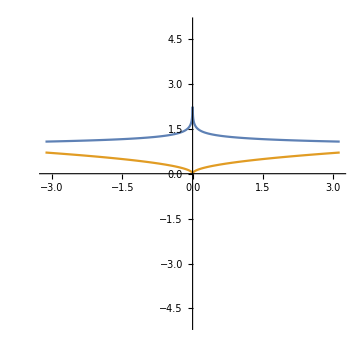

```mathematica
Plot[{(Abs[2π/θ])^(1/10),(Abs[2π/θ])^(-1/2)},{θ,-π,π},AspectRatio->1,PlotRange->5,ImageSize->Medium]
```

```mathematica
p=3;q=2;b=1;c=1;
Show[Boxer[6],Torus[{0,0},10,Pink],PunctureX[{0,0},Pink],ParametricPlot3D[{(2+Cos[p*t+b*2*π])*Cos[q*t+c*2*π],(2+Cos[p*t+b*2*π])*Sin[q*t+c*2*π],Sin[p*t+b*2*π]},{t,0,5*2*π},PlotRange->4,PlotStyle->{Thickness[.01],Purple},PlotPoints->100]]
```

-Graphics3D-

```mathematica
Manipulate[Show[{Boxer[{{-3,3},{-3,a},{-3,2}},500],Torus[{0,0,0},1,Pink]}],{a,2,3}]
```

Show::gcomb: Could not combine the graphics objects in Show[{Boxer[{{-3,3},{-3,2.993},{-3,2}},500],Torus[{0,0,0},1,RGBColor[1, 0.5, 0.5]]}].

```mathematica
Show[{Boxer[{{-3,3},{-3,2.3},{-3,2}},500],Torus[{0,0,0},1]}]
```

-Graphics3D-

```mathematica
Show[{Boxer[{{-3,3},{-3,2.7},{-3,2}},500],Torus[{0,0,0},1]}]
```

-Graphics3D-

```mathematica
p=3;q=2;b=1;c=1;
Show[Boxer[6],Torus[{0,0},4,Pink],PunctureY[{0,0},Pink],Longitudnal[{0,0,0}],Meridian[{0,0,0}]]
```

-Graphics3D-

```mathematica
center={0,0,0}; opacity=1;
ParametricPlot3D[(1/(θ+ϕ))^(1/1000){(2+Cos[ϕ])*Cos[θ]+center[[1]],(2+Cos[ϕ])*Sin[θ]+center[[2]],Sin[ϕ]},{θ,0,2*π},{ϕ,0,2*π},Mesh->None,PlotPoints->100,Boxed->False,Axes->False,ImageSize->Large,PlotStyle->{Opacity[opacity],color}]
```

-Graphics3D-